# Appendix D for ‘Rate enhancement of gated drift-diffusion process by optimal resetting’

Here we show the mathematical steps leading to the mean first passage time (MFPT) of a gated-drift diffusion process in bounded domain. A reflecting barrier is placed at x=L>x_0.  The theoretical formulation is given in Appendix D of the  paper. Here we show the exact way how we obtained the plots and the relevant mathematical quantities.

First we solve set of equations  Eq. (D.4) to obtain the co-efficients c_1,c_(2,)c_3,c_4.

```mathematica
FullSimplify[Solve[{c1 +c2+c3+c4+Q1inh==0,c1 m1 ⅇ^(m1 L)+c2 m2 ⅇ^(m2 L) +c3 m3 ⅇ^(m3 L) +c4 m4 ⅇ^(m4 L)==0,c1 m1 ⅇ^(m1 L)-α/β c2 m2 ⅇ^(m2 L) +c3 m3 ⅇ^(m3 L) -α/β c4 m4 ⅇ^(m4 L)==0,c1 m1 -α/β c2 m2 +c3 m3 -α/β c4 m4==0 },{c1,c2,c3,c4}],Assumptions->{L>0,Q1inh>0}]
```

Let us define these co-efficients separately as

```mathematica
c1:=(ⅇ^(L m3) (ⅇ^(L m2)-ⅇ^(L m4)) m2 m3 m4 Q1inh α)/(ⅇ^(L (m3+m4)) m3 m4 (m2 α+m1 β)-ⅇ^(L (m2+m3)) m2 m3 (m4 α+m1 β)-ⅇ^(L (m1+m4)) m1 m4 (m2 α+m3 β)+ⅇ^(L (m1+m2)) m1 m2 (m4 α+m3 β))
c2:=(ⅇ^(L m4) (ⅇ^(L m1)-ⅇ^(L m3)) m1 m3 m4 Q1inh β)/(ⅇ^(L (m3+m4)) m3 m4 (m2 α+m1 β)-ⅇ^(L (m2+m3)) m2 m3 (m4 α+m1 β)-ⅇ^(L (m1+m4)) m1 m4 (m2 α+m3 β)+ⅇ^(L (m1+m2)) m1 m2 (m4 α+m3 β))
c3:=(ⅇ^(L m1) (ⅇ^(L m2)-ⅇ^(L m4)) m1 m2 m4 Q1inh α)/(-ⅇ^(L (m3+m4)) m3 m4 (m2 α+m1 β)+ⅇ^(L (m2+m3)) m2 m3 (m4 α+m1 β)+ⅇ^(L (m1+m4)) m1 m4 (m2 α+m3 β)-ⅇ^(L (m1+m2)) m1 m2 (m4 α+m3 β))
c4:=(ⅇ^(L m2) (ⅇ^(L m1)-ⅇ^(L m3)) m1 m2 m3 Q1inh β)/(-ⅇ^(L (m3+m4)) m3 m4 (m2 α+m1 β)+ⅇ^(L (m2+m3)) m2 m3 (m4 α+m1 β)+ⅇ^(L (m1+m4)) m1 m4 (m2 α+m3 β)-ⅇ^(L (m1+m2)) m1 m2 (m4 α+m3 β))
```

Now we recall Eq. (A.5) to have the exact expression for the inhomogeneous (Q1inh, Q0inh) part of the Laplace transform of the survival probabilities Q_0, Q_1. These are given as

```mathematica
Q0inh:=1/(s+r)(1+r/(s+r+α+β)(α Q1 +(s+r+β)Q0))
Q1inh:=1/(s+r)(1+r/(s+r+α+β)(β Q0 +(s+r+α)Q1))
```

Using these expressions along with Eq. (D.2), Eq. (D.3) and the total survival probability as in Eq. (A.2), we have a self consistency equation for Q_0 and Q_1 with solutions

```mathematica
Simplify[Solve[{Q0==c1 ⅇ^(m1 x0)-α/β c2 ⅇ^(m2 x0)+c3 ⅇ^(m3 x0)-α/β c4 ⅇ^(m4 x0)+Q0inh,Q1==c1  ⅇ^(m1 x0)+c2  ⅇ^(m2 x0) +c3  ⅇ^(m3 x0) +c4  ⅇ^(m4 x0)+Q1inh},{Q0,Q1}],Assumptions->{L>x0>0,{m1,m2}<0,{m3,m4}>0}]
```

We now have exact expression for the survival probability in Laplace space with  m_1-m_4 given as

```mathematica
m1:=(λ-√(λ^2+4 DD (s+r)))/(2 DD)
m2:=(λ-√(λ^2+4 DD (α+β+s+r)))/(2 DD)
m3:=(λ+√(λ^2+4 DD (s+r)))/(2 DD)
m4:=(λ+√(λ^2+4 DD (α+β+s+r)))/(2 DD)
```

Note that diffusion co-efficient is denoted by DD.

Survival probability in Laplace space: Finally combining all the above results we have the exact expression for the survival probabilities Q_0 and Q_1 in Laplace variable s. Below we formally write those expressions in terms of the system parameters.

```mathematica
Q0:=(1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD (r+s+α+β)+λ^2)))/(2 DD)+L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) (r (α+β)+α (s+α+β)) (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD (r+s+α+β)+λ^2)))/(2 DD)+L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) (r (α+β)+α (s+α+β)) (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ-√(4 DD (r+s+α+β)+λ^2)))/(2 DD)+L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) (r (α+β)+α (s+α+β)) (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))+1/(8 DD^3)ⅇ^((x0 (λ-√(4 DD (r+s+α+β)+λ^2)))/(2 DD)+L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) (r (α+β)+α (s+α+β)) (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD (r+s)+λ^2)))/(2 DD)+L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) α (s+α+β) (λ-√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))+1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD (r+s)+λ^2)))/(2 DD)+L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) α (s+α+β) (λ-√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))+1/(8 DD^3)ⅇ^((x0 (λ-√(4 DD (r+s)+λ^2)))/(2 DD)+L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) α (s+α+β) (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ-√(4 DD (r+s)+λ^2)))/(2 DD)+L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) α (s+α+β) (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))+1/(4 DD^2)ⅇ^(L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) (s+α+β) (λ+√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2)) ((β (λ-√(4 DD (r+s)+λ^2)))/(2 DD)+(α (λ-√(4 DD (r+s+α+β)+λ^2)))/(2 DD))-1/(4 DD^2)ⅇ^(L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) (s+α+β) (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2)) ((β (λ+√(4 DD (r+s)+λ^2)))/(2 DD)+(α (λ-√(4 DD (r+s+α+β)+λ^2)))/(2 DD))-1/(4 DD^2)ⅇ^(L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) (s+α+β) (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) ((β (λ-√(4 DD (r+s)+λ^2)))/(2 DD)+(α (λ+√(4 DD (r+s+α+β)+λ^2)))/(2 DD))+1/(4 DD^2)ⅇ^(L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) (s+α+β) (λ-√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) ((β (λ+√(4 DD (r+s)+λ^2)))/(2 DD)+(α (λ+√(4 DD (r+s+α+β)+λ^2)))/(2 DD)))/(1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD (r+s+α+β)+λ^2)))/(2 DD)+L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) r s β (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD (r+s+α+β)+λ^2)))/(2 DD)+L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) r s β (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ-√(4 DD (r+s+α+β)+λ^2)))/(2 DD)+L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) r s β (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))+1/(8 DD^3)ⅇ^((x0 (λ-√(4 DD (r+s+α+β)+λ^2)))/(2 DD)+L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) r s β (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))+1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD (r+s)+λ^2)))/(2 DD)+L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) r α (s+α+β) (λ-√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD (r+s)+λ^2)))/(2 DD)+L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) r α (s+α+β) (λ-√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ-√(4 DD (r+s)+λ^2)))/(2 DD)+L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) r α (s+α+β) (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))+1/(8 DD^3)ⅇ^((x0 (λ-√(4 DD (r+s)+λ^2)))/(2 DD)+L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) r α (s+α+β) (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))+1/(4 DD^2)ⅇ^(L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) s (s+α+β) (λ+√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2)) ((β (λ-√(4 DD (r+s)+λ^2)))/(2 DD)+(α (λ-√(4 DD (r+s+α+β)+λ^2)))/(2 DD))-1/(4 DD^2)ⅇ^(L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) s (s+α+β) (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2)) ((β (λ+√(4 DD (r+s)+λ^2)))/(2 DD)+(α (λ-√(4 DD (r+s+α+β)+λ^2)))/(2 DD))-1/(4 DD^2)ⅇ^(L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) s (s+α+β) (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) ((β (λ-√(4 DD (r+s)+λ^2)))/(2 DD)+(α (λ+√(4 DD (r+s+α+β)+λ^2)))/(2 DD))+1/(4 DD^2)ⅇ^(L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) s (s+α+β) (λ-√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) ((β (λ+√(4 DD (r+s)+λ^2)))/(2 DD)+(α (λ+√(4 DD (r+s+α+β)+λ^2)))/(2 DD)))
```

```mathematica
Q1:=((s+α+β) (-1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD (r+s+α+β)+λ^2)))/(2 DD)+L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) β (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2))+1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD (r+s+α+β)+λ^2)))/(2 DD)+L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) β (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2))+1/(8 DD^3)ⅇ^((x0 (λ-√(4 DD (r+s+α+β)+λ^2)))/(2 DD)+L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) β (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ-√(4 DD (r+s+α+β)+λ^2)))/(2 DD)+L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) β (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD (r+s)+λ^2)))/(2 DD)+L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) α (λ-√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))+1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD (r+s)+λ^2)))/(2 DD)+L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) α (λ-√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))+1/(8 DD^3)ⅇ^((x0 (λ-√(4 DD (r+s)+λ^2)))/(2 DD)+L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) α (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ-√(4 DD (r+s)+λ^2)))/(2 DD)+L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) α (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))+1/(4 DD^2)ⅇ^(L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) (λ+√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2)) ((β (λ-√(4 DD (r+s)+λ^2)))/(2 DD)+(α (λ-√(4 DD (r+s+α+β)+λ^2)))/(2 DD))-1/(4 DD^2)ⅇ^(L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2)) ((β (λ+√(4 DD (r+s)+λ^2)))/(2 DD)+(α (λ-√(4 DD (r+s+α+β)+λ^2)))/(2 DD))-1/(4 DD^2)ⅇ^(L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) ((β (λ-√(4 DD (r+s)+λ^2)))/(2 DD)+(α (λ+√(4 DD (r+s+α+β)+λ^2)))/(2 DD))+1/(4 DD^2)ⅇ^(L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) (λ-√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) ((β (λ+√(4 DD (r+s)+λ^2)))/(2 DD)+(α (λ+√(4 DD (r+s+α+β)+λ^2)))/(2 DD))))/(1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD (r+s+α+β)+λ^2)))/(2 DD)+L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) r s β (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD (r+s+α+β)+λ^2)))/(2 DD)+L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) r s β (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ-√(4 DD (r+s+α+β)+λ^2)))/(2 DD)+L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) r s β (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))+1/(8 DD^3)ⅇ^((x0 (λ-√(4 DD (r+s+α+β)+λ^2)))/(2 DD)+L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) r s β (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))+1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD (r+s)+λ^2)))/(2 DD)+L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) r α (s+α+β) (λ-√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD (r+s)+λ^2)))/(2 DD)+L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) r α (s+α+β) (λ-√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ-√(4 DD (r+s)+λ^2)))/(2 DD)+L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) r α (s+α+β) (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))+1/(8 DD^3)ⅇ^((x0 (λ-√(4 DD (r+s)+λ^2)))/(2 DD)+L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) r α (s+α+β) (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2))+1/(4 DD^2)ⅇ^(L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) s (s+α+β) (λ+√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2)) ((β (λ-√(4 DD (r+s)+λ^2)))/(2 DD)+(α (λ-√(4 DD (r+s+α+β)+λ^2)))/(2 DD))-1/(4 DD^2)ⅇ^(L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ+√(4 DD (r+s+α+β)+λ^2))/(2 DD))) s (s+α+β) (λ-√(4 DD (r+s)+λ^2)) (λ+√(4 DD (r+s+α+β)+λ^2)) ((β (λ+√(4 DD (r+s)+λ^2)))/(2 DD)+(α (λ-√(4 DD (r+s+α+β)+λ^2)))/(2 DD))-1/(4 DD^2)ⅇ^(L ((λ+√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) s (s+α+β) (λ+√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) ((β (λ-√(4 DD (r+s)+λ^2)))/(2 DD)+(α (λ+√(4 DD (r+s+α+β)+λ^2)))/(2 DD))+1/(4 DD^2)ⅇ^(L ((λ-√(4 DD (r+s)+λ^2))/(2 DD)+(λ-√(4 DD (r+s+α+β)+λ^2))/(2 DD))) s (s+α+β) (λ-√(4 DD (r+s)+λ^2)) (λ-√(4 DD (r+s+α+β)+λ^2)) ((β (λ+√(4 DD (r+s)+λ^2)))/(2 DD)+(α (λ+√(4 DD (r+s+α+β)+λ^2)))/(2 DD)))
```

Mean first passage times: To find the mean first passage time we need to take the limit s->0 of the survival probabilities. Thus we have for T_0,

```mathematica
Series[Q0,{s,0,0},Assumptions->{L>0,α>0,β>0,x0>0,r>0,DD>0}]
T0[r_,x0_,L_,α_,β_,λ_,DD_]=FullSimplify[(-1/(8 DD^3)ⅇ^((2 L λ+x0 λ+L √(4 DD r+λ^2)-L √(4 DD r+4 DD α+4 DD β+λ^2)+x0 √(4 DD r+4 DD α+4 DD β+λ^2))/(2 DD)) (r (α+β)+α (α+β)) (λ-√(4 DD r+λ^2)) (λ+√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD r+4 DD α+4 DD β+λ^2)))/(2 DD)-(L (-2 λ+√(4 DD r+λ^2)+√(4 DD r+4 DD α+4 DD β+λ^2)))/(2 DD)) (r+α) (α+β) (λ-√(4 DD r+λ^2)) (λ+√(4 DD r+λ^2)) (-λ+√(4 DD r+4 DD α+4 DD β+λ^2))-1/(8 DD^3)ⅇ^((2 L λ+x0 λ-L √(4 DD r+λ^2)+L √(4 DD r+4 DD α+4 DD β+λ^2)-x0 √(4 DD r+4 DD α+4 DD β+λ^2))/(2 DD)) (r (α+β)+α (α+β)) (λ-√(4 DD r+λ^2)) (λ+√(4 DD r+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))+1/(8 DD^3)ⅇ^((2 L λ+x0 λ+L √(4 DD r+λ^2)+L √(4 DD r+4 DD α+4 DD β+λ^2)-x0 √(4 DD r+4 DD α+4 DD β+λ^2))/(2 DD)) (r (α+β)+α (α+β)) (λ-√(4 DD r+λ^2)) (λ+√(4 DD r+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))+1/(8 DD^3)ⅇ^((2 L λ+x0 λ-L √(4 DD r+λ^2)+x0 √(4 DD r+λ^2)+L √(4 DD r+4 DD α+4 DD β+λ^2))/(2 DD)) α (α+β) (λ-√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD r+λ^2)))/(2 DD)-(L (-2 λ+√(4 DD r+λ^2)+√(4 DD r+4 DD α+4 DD β+λ^2)))/(2 DD)) α (α+β) (λ-√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))+1/(8 DD^3)ⅇ^((2 L λ+x0 λ+L √(4 DD r+λ^2)-x0 √(4 DD r+λ^2)-L √(4 DD r+4 DD α+4 DD β+λ^2))/(2 DD)) α (α+β) (λ+√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))-1/(8 DD^3)ⅇ^((2 L λ+x0 λ+L √(4 DD r+λ^2)-x0 √(4 DD r+λ^2)+L √(4 DD r+4 DD α+4 DD β+λ^2))/(2 DD)) α (α+β) (λ+√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))+1/(8 DD^3)ⅇ^((L (2 λ+√(4 DD r+λ^2)+√(4 DD r+4 DD α+4 DD β+λ^2)))/(2 DD)) (α+β) (λ+√(4 DD r+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2)) (α λ+β λ-β √(4 DD r+λ^2)-α √(4 DD r+4 DD α+4 DD β+λ^2))-1/(8 DD^3)ⅇ^((L (2 λ-√(4 DD r+λ^2)+√(4 DD r+4 DD α+4 DD β+λ^2)))/(2 DD)) (α+β) (λ-√(4 DD r+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2)) (α λ+β λ+β √(4 DD r+λ^2)-α √(4 DD r+4 DD α+4 DD β+λ^2))-1/(8 DD^3)ⅇ^((L (2 λ+√(4 DD r+λ^2)-√(4 DD r+4 DD α+4 DD β+λ^2)))/(2 DD)) (α+β) (λ+√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (α λ+β λ-β √(4 DD r+λ^2)+α √(4 DD r+4 DD α+4 DD β+λ^2))+1/(8 DD^3)ⅇ^(-(L (-2 λ+√(4 DD r+λ^2)+√(4 DD r+4 DD α+4 DD β+λ^2)))/(2 DD)) (α+β) (λ-√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (α λ+β λ+β √(4 DD r+λ^2)+α √(4 DD r+4 DD α+4 DD β+λ^2)))/(-1/(8 DD^3)ⅇ^((2 L λ+x0 λ-L √(4 DD r+λ^2)+x0 √(4 DD r+λ^2)+L √(4 DD r+4 DD α+4 DD β+λ^2))/(2 DD)) r α (α+β) (λ-√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))+1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD r+λ^2)))/(2 DD)-(L (-2 λ+√(4 DD r+λ^2)+√(4 DD r+4 DD α+4 DD β+λ^2)))/(2 DD)) r α (α+β) (λ-√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))-1/(8 DD^3)ⅇ^((2 L λ+x0 λ+L √(4 DD r+λ^2)-x0 √(4 DD r+λ^2)-L √(4 DD r+4 DD α+4 DD β+λ^2))/(2 DD)) r α (α+β) (λ+√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))+1/(8 DD^3)ⅇ^((2 L λ+x0 λ+L √(4 DD r+λ^2)-x0 √(4 DD r+λ^2)+L √(4 DD r+4 DD α+4 DD β+λ^2))/(2 DD)) r α (α+β) (λ+√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))),Assumptions->{L>0,α>0,β>0,x0>0,r>0,DD>0,λ>0}]
```

and similarly for T_1,

```mathematica
Series[Q1,{s,0,0},Assumptions->{L>0,α>0,β>0,x0>0,r>0,DD>0}]
```

```mathematica
T1[r_,x0_,L_,α_,β_,λ_,DD_]=FullSimplify[((α+β) (1/(8 DD^3)ⅇ^((2 L λ+x0 λ+L √(4 DD r+λ^2)-L √(4 DD r+4 DD α+4 DD β+λ^2)+x0 √(4 DD r+4 DD α+4 DD β+λ^2))/(2 DD)) β (λ-√(4 DD r+λ^2)) (λ+√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD r+4 DD α+4 DD β+λ^2)))/(2 DD)-(L (-2 λ+√(4 DD r+λ^2)+√(4 DD r+4 DD α+4 DD β+λ^2)))/(2 DD)) β (λ-√(4 DD r+λ^2)) (λ+√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2))+1/(8 DD^3)ⅇ^((2 L λ+x0 λ-L √(4 DD r+λ^2)+L √(4 DD r+4 DD α+4 DD β+λ^2)-x0 √(4 DD r+4 DD α+4 DD β+λ^2))/(2 DD)) β (λ-√(4 DD r+λ^2)) (λ+√(4 DD r+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))-1/(8 DD^3)ⅇ^((2 L λ+x0 λ+L √(4 DD r+λ^2)+L √(4 DD r+4 DD α+4 DD β+λ^2)-x0 √(4 DD r+4 DD α+4 DD β+λ^2))/(2 DD)) β (λ-√(4 DD r+λ^2)) (λ+√(4 DD r+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))+1/(8 DD^3)ⅇ^((2 L λ+x0 λ-L √(4 DD r+λ^2)+x0 √(4 DD r+λ^2)+L √(4 DD r+4 DD α+4 DD β+λ^2))/(2 DD)) α (λ-√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))-1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD r+λ^2)))/(2 DD)-(L (-2 λ+√(4 DD r+λ^2)+√(4 DD r+4 DD α+4 DD β+λ^2)))/(2 DD)) α (λ-√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))+1/(8 DD^3)ⅇ^((2 L λ+x0 λ+L √(4 DD r+λ^2)-x0 √(4 DD r+λ^2)-L √(4 DD r+4 DD α+4 DD β+λ^2))/(2 DD)) α (λ+√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))-1/(8 DD^3)ⅇ^((2 L λ+x0 λ+L √(4 DD r+λ^2)-x0 √(4 DD r+λ^2)+L √(4 DD r+4 DD α+4 DD β+λ^2))/(2 DD)) α (λ+√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))+1/(8 DD^3)ⅇ^((L (2 λ+√(4 DD r+λ^2)+√(4 DD r+4 DD α+4 DD β+λ^2)))/(2 DD)) (λ+√(4 DD r+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2)) (α λ+β λ-β √(4 DD r+λ^2)-α √(4 DD r+4 DD α+4 DD β+λ^2))-1/(8 DD^3)ⅇ^((L (2 λ-√(4 DD r+λ^2)+√(4 DD r+4 DD α+4 DD β+λ^2)))/(2 DD)) (λ-√(4 DD r+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2)) (α λ+β λ+β √(4 DD r+λ^2)-α √(4 DD r+4 DD α+4 DD β+λ^2))-1/(8 DD^3)ⅇ^((L (2 λ+√(4 DD r+λ^2)-√(4 DD r+4 DD α+4 DD β+λ^2)))/(2 DD)) (λ+√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (α λ+β λ-β √(4 DD r+λ^2)+α √(4 DD r+4 DD α+4 DD β+λ^2))+1/(8 DD^3)ⅇ^(-(L (-2 λ+√(4 DD r+λ^2)+√(4 DD r+4 DD α+4 DD β+λ^2)))/(2 DD)) (λ-√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (α λ+β λ+β √(4 DD r+λ^2)+α √(4 DD r+4 DD α+4 DD β+λ^2))))/(-1/(8 DD^3)ⅇ^((2 L λ+x0 λ-L √(4 DD r+λ^2)+x0 √(4 DD r+λ^2)+L √(4 DD r+4 DD α+4 DD β+λ^2))/(2 DD)) r α (α+β) (λ-√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))+1/(8 DD^3)ⅇ^((x0 (λ+√(4 DD r+λ^2)))/(2 DD)-(L (-2 λ+√(4 DD r+λ^2)+√(4 DD r+4 DD α+4 DD β+λ^2)))/(2 DD)) r α (α+β) (λ-√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))-1/(8 DD^3)ⅇ^((2 L λ+x0 λ+L √(4 DD r+λ^2)-x0 √(4 DD r+λ^2)-L √(4 DD r+4 DD α+4 DD β+λ^2))/(2 DD)) r α (α+β) (λ+√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))+1/(8 DD^3)ⅇ^((2 L λ+x0 λ+L √(4 DD r+λ^2)-x0 √(4 DD r+λ^2)+L √(4 DD r+4 DD α+4 DD β+λ^2))/(2 DD)) r α (α+β) (λ+√(4 DD r+λ^2)) (λ-√(4 DD r+4 DD α+4 DD β+λ^2)) (λ+√(4 DD r+4 DD α+4 DD β+λ^2))),Assumptions->{L>0,α>0,β>0,x0>0,r>0,DD>0,λ>0}]
```

The overall MFPT by taking contribution from both T_0 and T_1 is given as,

```mathematica
Tav[r_,x0_,L_,α_,β_,λ_,DD_]=FullSimplify[β/(α+β)T0[r,x0,L,α,β,λ,DD]+α/(α+β)T1[r,x0,L,α,β,λ,DD],Assumptions->{L>0,α>0,β>0,x0>0,r>0,DD>0,λ>0}]
```

Below we show the behaviour of the MFPT T_av as shown in the paper.

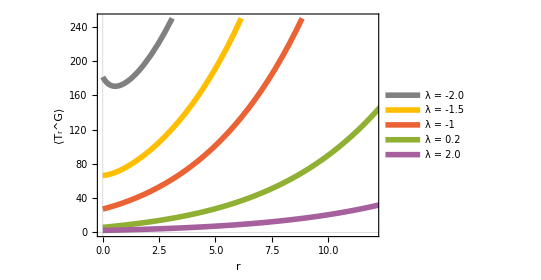

```mathematica
Show[Plot[{Tav[r,2,3,0.5,0.5,-2,1],Tav[r,2,3,0.5,0.5,-1.5,1],Tav[r,2,3,0.5,0.5,-1,1],Tav[r,2,3,0.5,0.5,0.2,1],Tav[r,2,3,0.5,0.5,2,1]},{r,0.0001,15},PlotRange-> {{0,12},{0,250}}, Frame-> True,FrameLabel-> {"r","⟨T_r^G⟩"},FrameStyle-> Directive[Black,Thickness[0.0025]],PlotTheme->"Scientific",PlotLegends->Placed[{"λ = -2.0",
  "λ = -1.5","λ = -1","λ = 0.2","λ = 2.0"},{0.85,0.42}],{Background-> White}, PlotStyle->{{Gray,Solid,AbsoluteThickness[4]},{ColorData[97,"ColorList"][[8]],Solid,AbsoluteThickness[4]},{ColorData[97,"ColorList"][[4]],Solid,AbsoluteThickness[4]},{ColorData[97,"ColorList"][[3]],Solid,AbsoluteThickness[4]},{ColorData[97,"ColorList"][[9]],Solid,AbsoluteThickness[4]}},LabelStyle->Directive[FontFamily->"Courier",20,GrayLevel[0],Bold]],AspectRatio-> 0.7]
```